```mathematica
raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2025-03-20_oneBunch_linac_phase_amp_jitter_jitter_reference.csv"];
headers = raw[[1]]
```

{L0BPhaseSet,L1PhaseSet,L2PhaseSet,L3PhaseSet,L0BEnergyOffset,L1EnergyOffset,L2EnergyOffset,L3EnergyOffset,Unique ID,xopt_runtime,xopt_error}

```mathematica
data = Dataset[AssociationThread[headers,#]&/@raw[[2;;]]];
```

```mathematica
Mean[data[[All,"L0BPhaseSet"]]]
```

-15.

```mathematica
StandardDeviation[data[[All,"L0BPhaseSet"]]]
```

0.0328863

```mathematica
Mean[data[[All,"L1PhaseSet"]]]
```

-14.8498

```mathematica
StandardDeviation[data[[All,"L1PhaseSet"]]]
```

0.230206

```mathematica
Mean[data[[All,"L2PhaseSet"]]]
```

-35.8

```mathematica
StandardDeviation[data[[All,"L2PhaseSet"]]]
```

0.131546

```mathematica
Mean[data[[All,"L3PhaseSet"]]]
```

3.67937×10^-6

```mathematica
StandardDeviation[data[[All,"L3PhaseSet"]]]
```

0.13154

```mathematica
Mean[data[[All,"L3EnergyOffset"]]]
```

623.661

```mathematica
StandardDeviation[data[[All,"L3EnergyOffset"]]]
```

5.42624×10^6

```mathematica
Length[data[[All,"L0BPhaseSet"]]]
```

50040

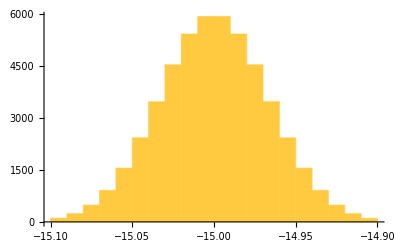

```mathematica
Histogram[data[[All,"L0BPhaseSet"]]]
```